# De ecuaciones a código

## Estructuras de datos y loops

## Estructuras de datos

En ciencias de la computación, las estructuras de datos son formas de organizar y almacenar datos para que puedan utilizarse de manera eficiente . Definen cómo se organizan los datos en la memoria y cómo se realizan operaciones como el acceso, la inserción, la eliminación y la búsqueda .

En esta sección estudiaremos las estructuras de datos más importantes en Wolfram Language.

### Listas

Una lista es una colección ordenada de elementos encerrados entre llaves { }. Sus elementos pueden ser de cualquier tipo: números, símbolos, expresiones, e incluso otras listas.

```mathematica
lista={3.14,2.72,"hola","mundo",x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}
```

{3.14,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}

#### Estructura de listas

Podemos acceder a cada elemento de una lista usando la notación de doble corchete ⟦ ⟧. A cada elemento le corresponde un índice comenzando desde el 1 hacia adelante.

```mathematica
Grid[#,
Spacings->{2,1},
Frame->{None,None,{{2,2},{2,Length[#[[2]]]}}->True},
ItemStyle->{Automatic,{Directive[Orange,Bold,FontSize->12]}}
]&@
({Prepend[Range[Length[#]],Null],Prepend[#,"lista ="]}&@lista)
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100
lista = | 7 | 23 | 29 | 65 | 52 | 25 | 30 | 10 | 22 | 31 | 15 | 17 | 5 | 56 | 42 | 25 | 27 | 30 | 15 | 5 | 12 | 16 | 9 | 12 | 13 | 38 | 73 | 28 | 17 | 37 | 84 | 1 | 53 | 44 | 18 | 32 | 7 | 7 | 19 | 10 | 27 | 6 | 22 | 22 | 26 | 5 | 21 | 69 | 24 | 25 | 24 | 34 | 15 | 17 | 16 | 4 | 9 | 4 | 53 | 25 | 18 | 38 | 20 | 4 | 38 | 17 | 44 | 2 | 12 | 40 | 28 | 26 | 19 | 21 | 17 | 52 | 4 | 18 | 8 | 1 | 18 | 45 | 9 | 4 | 84 | 1 | 45 | 13 | 25 | 15 | 55 | 29 | 51 | 22 | 1 | 60 | 9 | 1 | 15 | 25

```mathematica
lista[[1]]
```

3.14

```mathematica
lista[[7]]
```

{10,20}

```mathematica
lista[[7,1]]
```

10

```mathematica
lista[[-1]]
```

Cos[b]

```mathematica
lista[[{1,3,8}]]
```

{3.14,hola,{{30,40},{40,50}}}

```mathematica
lista[[2;;4]]
```

{2.72,hola,mundo}

```mathematica
lista[[2;;7;;2]]
```

{2.72,mundo,y}

```mathematica
lista[[;;;;2]]
```

{3.14,hola,x,{10,20},Sin[a]}

Al acceder a los elementos de una lista también podemos sustituir los valores que se encuentran en cada posición.

```mathematica
lista
```

{3.14,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}

```mathematica
lista[[1]]=π
```

π

```mathematica
lista
```

{π,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}

Syntactic sugar

```mathematica
List[1,2,3]=={1,2,3}
```

True

Además de los ⟦ ⟧ tenemos otro tipo de operaciones especificas de listas para seleccionar elementos

```mathematica
First[lista]
```

π

```mathematica
Last[lista]
```

Cos[b]

```mathematica
Rest[lista]
```

{2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}

```mathematica
Most[lista]
```

{π,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a]}

```mathematica
Take[lista,4]
```

{π,2.72,hola,mundo}

```mathematica
Drop[lista,4]
```

{x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}

```mathematica
Drop[lista,-4]
```

{π,2.72,hola,mundo,x,y}

#### Manipulación de listas

Podemos añadir valores a las listas usando:

```mathematica
Append[lista,γ]
```

{π,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b],γ}

```mathematica
Prepend[lista,α]
```

{α,π,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}

```mathematica
Insert[lista,σ,6]
```

{π,2.72,hola,mundo,x,σ,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b]}

```mathematica
Delete[lista,7]
```

{π,2.72,hola,mundo,x,y,{{30,40},{40,50}},Sin[a],Cos[b]}

```mathematica
DeleteDuplicates[{4,4,5,2,3,3,1,5,1,1}]
```

{4,5,2,3,1}

Y sus versiones de programación procedural.

Además podemos usar otras funciones sobre nuestras listas

```mathematica
Length[lista]
```

10

```mathematica
Length[lista[[8]]]
```

2

```mathematica
Dimensions[lista]
```

{10}

```mathematica
Dimensions[lista[[8]]]
```

{2,2}

```mathematica
ArrayDepth[lista]
```

1

```mathematica
ArrayDepth[lista[[8]]]
```

2

```mathematica
Flatten[lista]
```

{π,2.72,hola,mundo,x,y,10,20,30,40,40,50,Sin[a],Cos[b]}

```mathematica
Join[lista,{i,j,k}]
```

{π,2.72,hola,mundo,x,y,{10,20},{{30,40},{40,50}},Sin[a],Cos[b],i,j,k}

```mathematica
Partition[lista,2]
```

{{π,2.72},{hola,mundo},{x,y},{{10,20},{{30,40},{40,50}}},{Sin[a],Cos[b]}}

```mathematica
Reverse[lista]
```

{Cos[b],Sin[a],{{30,40},{40,50}},{10,20},y,x,mundo,hola,2.72,π}

```mathematica
Sort[lista]
```

{2.72,hola,mundo,π,x,y,Cos[b],{10,20},{{30,40},{40,50}},Sin[a]}

#### Operación de listas

```mathematica
lista={2,6/7,π,ⅈ};
```

```mathematica
lista+1
```

{3,13/7,1+π,1+ⅈ}

```mathematica
lista+{1,2,3,4}
```

{3,20/7,3+π,4+ⅈ}

```mathematica
2*lista
```

{4,12/7,2 π,2 ⅈ}

```mathematica
{1,2,3,4}*lista
```

{2,12/7,3 π,4 ⅈ}

```mathematica
lista^2
```

{4,36/49,π^2,-1}

```mathematica
lista^{1,2,3,4}
```

{2,36/49,π^3,1}

```mathematica
Exp[lista]
```

{ⅇ^2,ⅇ^(6/7),ⅇ^π,ⅇ^ⅈ}

```mathematica
Sin[lista]
```

{Sin[2],Sin[6/7],0,ⅈ Sinh[1]}

```mathematica
Log[lista]
```

{Log[2],-Log[7/6],Log[π],(ⅈ π)/2}

```mathematica
Total[lista]
```

(20/7+ⅈ)+π

#### Estadística

```mathematica
lista={7,23,29,65,52,25,30,10,22,31,15,17,5,56,42,25,27,30,15,5,12,16,9,12,13,38,73,28,17,37,84,1,53,44,18,32,7,7,19,10,27,6,22,22,26,5,21,69,24,25,24,34,15,17,16,4,9,4,53,25,18,38,20,4,38,17,44,2,12,40,28,26,19,21,17,52,4,18,8,1,18,45,9,4,84,1,45,13,25,15,55,29,51,22,1,60,9,1,15,25};
```

```mathematica
Min[lista]
```

1

```mathematica
Max[lista]
```

84

```mathematica
Mean[lista]
```

2463/100

```mathematica
N[Mean[lista]]
```

24.63

```mathematica
StandardDeviation[lista]
```

(√(3459331/11))/30

```mathematica
StandardDeviation[lista]//N
```

18.693

#### Creación de listas

```mathematica
?Range
```

```mathematica
Range[0,7]
```

{0,1,2,3,4,5,6,7}

```mathematica
?Table
```

```mathematica
Table[i^2,{i,1,10}]
```

{1,16,49,100}

```mathematica
?Array
```

```mathematica
Array[f,{5,2}]
```

{{f[1,1],f[1,2]},{f[2,1],f[2,2]},{f[3,1],f[3,2]},{f[4,1],f[4,2]},{f[5,1],f[5,2]}}

```mathematica
?ConstantArray
```

```mathematica
ConstantArray[a,{3,3}]
```

{{a,a,a},{a,a,a},{a,a,a}}

```mathematica
?CenterArray
```

```mathematica
CenterArray[1,{3,3}]
```

{{0,0,0},{0,1,0},{0,0,0}}

### Asociaciones

```mathematica
asoc=<|"nombre"->"Mariana","apellido"->"Pérez","edad"->24,color->RGBColor["Teal"],1->7,π->6|>
```

<|nombre→Mariana,apellido→Pérez,edad→24,color→RGBColor[0., 0.5019607843137255, 0.5019607843137255],1→7,π→6|>

Las asociaciones son el equivalente a un diccionario en otros lenguajes y nos permiten acceder a valores por medio de llaves.

```mathematica
asoc["nombre"]
```

Mariana

```mathematica
asoc[["nombre"]]
```

Mariana

```mathematica
asoc[color]
```

RGBColor[0., 0.5019607843137255, 0.5019607843137255]

```mathematica
asoc[[color]]
```

Part::pkspec1: The expression color cannot be used as a part specification.

<|nombre→Mariana,apellido→Pérez,edad→24,color→RGBColor[0., 0.5019607843137255, 0.5019607843137255]|>⟦color⟧

```mathematica
asoc[1]
```

7

```mathematica
asoc[[1]]
```

Mariana

```mathematica
asoc[π]
```

6

```mathematica
asoc[[π]]
```

Part::pkspec1: The expression π cannot be used as a part specification.

<|nombre→Mariana,apellido→Pérez,edad→24,color→RGBColor[0., 0.5019607843137255, 0.5019607843137255],1→7,π→6|>⟦π⟧

```mathematica
Keys[asoc]
```

{nombre,apellido,edad,color}

```mathematica
Values[asoc]
```

{Mariana,Pérez,24,RGBColor[0., 0.5019607843137255, 0.5019607843137255]}

```mathematica
Lookup[asoc,"cumpleaños"]
```

Missing[KeyAbsent,cumpleaños]

```mathematica
KeySort[asoc]
```

<|apellido→Pérez,color→RGBColor[0., 0.5019607843137255, 0.5019607843137255],edad→24,nombre→Mariana|>

### Expresiones

```mathematica
expr=a x^2+b x+c+f[x]+d g[x]
```

c+b x+a x^2+f[x]+d g[x]

Las expresiones de Mathematica son en sí mismas una estructura de datos que se puede manipular en el propio lenguaje.

```mathematica
expr//FullForm
```

Plus[c,Times[b,x],Times[a,Power[x,2]],f[x],Times[d,g[x]]]

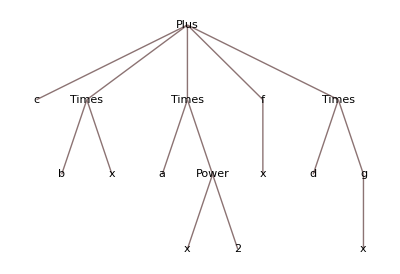

```mathematica
expr//TreeForm
```

```mathematica
expr[[1]]
```

c

```mathematica
expr[[5]]
```

d g[x]

```mathematica
expr[[5,2]]
```

g[x]

```mathematica
expr[[5,2,1]]
```

x

```mathematica
expr//Length
```

5

### Datasets

```mathematica
data=Dataset[{
<|"class"->"3rd","age"->19,"sex"->"male","survived"->False|>,<|"class"->"1st","age"->Missing[],"sex"->"female","survived"->True|>,<|"class"->"3rd","age"->39,"sex"->"male","survived"->False|>,<|"class"->"1st","age"->18,"sex"->"male","survived"->False|>,<|"class"->"1st","age"->48,"sex"->"male","survived"->False|>,<|"class"->"1st","age"->30,"sex"->"female","survived"->True|>,<|"class"->"2nd","age"->20,"sex"->"male","survived"->True|>,<|"class"->"3rd","age"->32,"sex"->"male","survived"->False|>,<|"class"->"3rd","age"->39,"sex"->"male","survived"->False|>,<|"class"->"1st","age"->23,"sex"->"female","survived"->True|>
}]
```

Los Datasets son conjuntos de datos organizados especializados para el análisis de datos.

```mathematica
Query[All,"class"]@data
```

```mathematica
Query[Select[#sex=="male"&],"age"]@data
```

```mathematica
Query[All,{"class","survived"}]@data
```

Estos pueden ser más complicados que simplemente datos tabulares al costo de una menor eficiencia computacional.

```mathematica
ExampleData[{"Dataset","StatePopulations"}]
```

### Más estructuras de datos

Además de eso tenemos estructuras de datos más variadas que solo se comentarán y se mostrará un ejemplo, pero no se detallarán

Para arreglos de datos con pocos elementos relativos al tamaño del mismo

```mathematica
SparseArray[{{i_,i_}->-2,{i_,j_}/;Abs[i-j]==1->1},{5,5}]
```

SparseArray[…]

Para operaciones más eficientes con tipos de datos «estándar»

```mathematica
NumericArray[Table[2^i-1,{i,0,8}],"UnsignedInteger8"]
```

NumericArray[…]

```mathematica
Graph[Table[i->Mod[i^2,74],{i,100}]]
```

-Graphics-

Para representar datos jerarquizados

```mathematica
Tree[a,{Tree[b,{c,d}],e,f}]
```

-Graphics-

Y de manera más general una gran variedad de estructuras nativas que podemos usar en Mathematica

```mathematica
CreateDataStructure["Stack"]
```

DataStructure[…]

Esta es la alternativa a Dataset que solo representa datos tabulares, pero con operaciones más eficientes. Al haber salido en la ultima versión de Mathematica solo la mencionaremos por completitud con los ejemplos anteriores

```mathematica
Tabular[]
```

Tabular[]

## Bucles

### Do

```mathematica
?Do
```

Similar a un Table, con la diferencia de que no devuelve nada por sí mismo.

```mathematica
Do[i^2,{i,1,10}]
```

En el caso en el que se desea generar una lista como resultado, Table lo hace directamente, mientras que Do solo puede modificar listas previamente existentes.

```mathematica
Module[{cuadrados},
cuadrados={};
Do[
AppendTo[cuadrados,i^2],
{i,1,10}
];
cuadrados
]
```

{1,4,9,16,25,36,49,64,81,100}

Útil cuando se quiere obtener el resultado final después de repetir una acción, sin recolectar resultados intermedios.

```mathematica
Module[{a,b},
{a,b}={0,1};
Do[
{a,b}={b,a+b},
10-1];
b
]
```

55

#### Comparación Do vs. Table

Cuál es mejor depende de la tarea que se quiere realizar. En el caso de crear listas, Table es por lo general la mejor opción pues crea una lista como resultado directamente y se usa naturalmente con otras funciones funcionales (que se verán en la próxima clase). Además, el código con Table suele ser más corto y claro.

```mathematica
RepeatedTiming[Table[i^2,{i,1,10}];]
```

{3.42013×10^-6,Null}

```mathematica
RepeatedTiming[
Module[{cuadrados},
cuadrados={};
Do[
AppendTo[cuadrados,i^2],
{i,1,10}
];
cuadrados];
]
```

{0.0000126373,Null}

A pesar de lo anterior, Do puede ser más rápido en situaciones donde solo se requiera el resultado final luego de repetir una acción.

```mathematica
RepeatedTiming[
Last@Module[{a,b},
{a,b}={0,1};
Table[
{a,b}={b,a+b};
a,
{10-1}]
];
]
```

{0.0000125707,Null}

```mathematica
RepeatedTiming[
Module[{a,b},
{a,b}={0,1};
Do[
{a,b}={b,a+b},
10-1];
b;
]
]
```

{9.93027×10^-6,Null}

### While

```mathematica
?While
```

Repite una acción mientras se cumpla una condición. Tampoco devuelve nada por sí mismo.

```mathematica
Module[{cuadrados},
cuadrados={};
i=1;
While[
i<=10,
AppendTo[cuadrados,i^2];
i++
];
cuadrados]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Module[{a,b,i},{a,b}={0,1};
i=1;
While[
i<10,
{a,b}={b,a+b};
i++];
b]
```

55

### For

```mathematica
?For
```

Combina inicialización, condición y actualización en una sola línea . Tampoco devuelve nada por sí mismo.

```mathematica
Module[{cuadrados},
cuadrados={};
For[i=1,i<=10,i++,
AppendTo[cuadradosFor,i^2]
];
cuadradosFor]
```

{1,4,9,16,25,36,49,64,81,100}

### ¿Por qué se prefiere Table?

Mathematica está optimizado internamente para operaciones funcionales.
Table se usa naturalmente con otras funciones, como se verá en la siguiente clase.